```mathematica
ClearAll["Global`*"]
```

## Import spectrum computation from C++ result

Browse the Data folder to find a suitable computation

```mathematica
fofile=FileNames[StringJoin[ParentDirectory[NotebookDirectory[]],"/data/examplescenario/freezeout.csv"]];
folders=FileNames[StringJoin[ParentDirectory[NotebookDirectory[]],"/data/examplescenario/primaryspec/*"]];
Print[Length[folders]," files found"]
```

300 files found

...and choose one file for testing.

{{# 20250605_114044},{# initdata:	data/examplescenario/initdata.csv},{# freezeout file: 	data/examplescenario/freezeout.csv},{# particle mass:	1.71429},{# NpT:	400},{# pTmax:	4},{# epsabs:	0},{# epsrel:	1e-05},{# integr iter:	10000}}

primespec header:
# 20250605_114044
# initdata:	data/examplescenario/initdata.csv
# freezeout file: 	data/examplescenario/freezeout.csv
# particle mass:	1.71429
# NpT:	400
# pTmax:	4
# epsabs:	0
# epsrel:	1e-05
# integr iter:	10000
(...)

initfile header:
# 20250605_114044 |  |  |  | 
alpha | Re@phiIm@phi | Re@DphiIm@Dphi |  | 
0 | 0.1 | 0 | 0 | 0
0.00157237 | 0.1 | 0 | 0 | 0
0.00314474 | 0.1 | 0 | 0 | 0
(...)

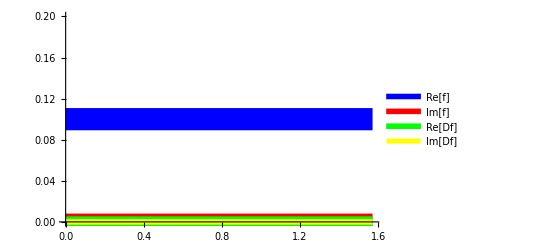

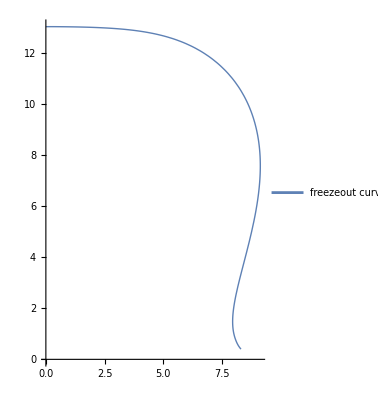

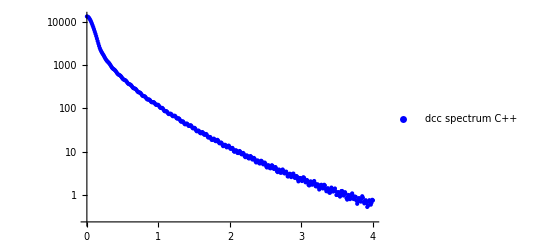

```mathematica
cppspecfolder=folders[[251]];
dataprimespec=Import[StringJoin[cppspecfolder,"/spectr.txt"],"CSV"];
datainitfield=Import[StringJoin[cppspecfolder,"/initialfields.txt"],"CSV"];

primespechead=dataprimespec[[1;;9]]
Print["primespec header:\n",TableForm[primespechead],"\n(...)"]
Print["initfile header:\n",TableForm[datainitfield[[1;;5]]],"\n(...)"]
qTscpp=Transpose[dataprimespec[[11;;]]][[1]];
primespeclistcpp=Transpose[dataprimespec[[11;;]]][[2]];

initalpha=Transpose[datainitfield[[3;;]]][[1]];
initfuncRe=Transpose[datainitfield[[3;;]]][[2]];
initfuncIm=Transpose[datainitfield[[3;;]]][[3]];
initDfuncRe=Transpose[datainitfield[[3;;]]][[4]];
initDfuncIm=Transpose[datainitfield[[3;;]]][[5]];
initfunc=Interpolation[Transpose@{initalpha,initfuncRe+I*initfuncIm}];
initDfunc=Interpolation[Transpose@{initalpha,initDfuncRe+I*initDfuncIm}];
Show[
Plot[Re@initfunc[α],{α,0,π/2},PlotLegends->{Re@f},PlotStyle->{Blue,Thickness[0.04]}],
Plot[Im@initfunc[α],{α,0,π/2},PlotLegends->{Im@f},PlotStyle->{Red,Thickness[0.03]}],
Plot[Re@initDfunc[α],{α,0,π/2},PlotLegends->{Re@Df},PlotStyle->{Green,Thickness[0.02]}],
Plot[Im@initDfunc[α],{α,0,π/2},PlotLegends->{Im@Df},PlotStyle->{Yellow,Thickness[0.01]}]
]

fodata=Import[fofile[[1]]];
headers=fodata[[1]];
fofields=Transpose@fodata[[2;;]];
αs=fofields[[1]];
τs=fofields[[2]];
rs=fofields[[3]];
Dτs=fofields[[4]];
Drs=fofields[[5]];

r=Interpolation[Transpose@{αs,rs}];
Dr=Interpolation[Transpose@{αs,Drs}];
τ=Interpolation[Transpose@{αs,τs}];
Dτ=Interpolation[Transpose@{αs,Dτs}];

curve[α_]:={r[α],τ[α]};
ParametricPlot[curve[α],{α,0,π/2},PlotStyle->Thick,PlotRange->Automatic,PlotLegends->{"freezeout curve"}]

ListLogPlot[Transpose@{qTscpp,primespeclistcpp},PlotLegends->{"dcc spectrum C++"},PlotStyle->Blue]
```

## Perform the dcc spec computation in Mathematica

```mathematica
ComputeDCCSpec[m_,ps_,f_,Df_,anti_]:=Module[{ωs,J0rp,J1rp,Y0tw,Y1tw,J0tw,J1tw,plusminus,G0,G1,Jp},
(*
f is supposed to be the condensate field, Df it's perpendicular derivative, 
Df = r'*D[f,τ]+τ'*D[f,r]
*)
GeVtoIfm=5.0677;(*5.0677;(*1GeV=5.0677(fm^-1)\[hbar]c*)*)
IfmtoGeV=1/GeVtoIfm;
fmtoIGeV=GeVtoIfm;
IGeVtofm=1/fmtoIGeV;

ωs=Sqrt[ps^2+m^2];(*in GeV (p in GeV) *)
J0rp[α_]=BesselJ[0,r[α]*ps*GeVtoIfm];(*dimensionless*)
J1rp[α_]=BesselJ[1,r[α]*ps*GeVtoIfm];(*dimensionless*)
Y0tw[α_]=BesselY[0,τ[α]*ωs*GeVtoIfm];(*dimensionless*)
Y1tw[α_]=BesselY[1,τ[α]*ωs*GeVtoIfm];(*dimensionless*)
J0tw[α_]=BesselJ[0,τ[α]*ωs*GeVtoIfm];(*dimensionless*)
J1tw[α_]=BesselJ[1,τ[α]*ωs*GeVtoIfm];(*dimensionless*)

plusminus=If[anti,-1,+1];

G0[α_]=J0rp[α]*(-Y0tw[α]+plusminus*I*J0tw[α]);(*dimensionless*)
G1[α_]=Dτ[α]*fmtoIGeV*ps*J1rp[α]*(-Y0tw[α]+plusminus*I*J0tw[α])+(*dimensionless*)
Dr[α]*fmtoIGeV*ωs*J0rp[α]*(-Y1tw[α]+plusminus*I*J1tw[α]);(*dimensionless*)

Jp=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*(Df[α]*G0[α]+f[α]*G1[α]),{α,0,π/2},
Method->{Automatic,"SymbolicProcessing"->0}
];
0.5*Abs[Jp]^2/(2*π)^3
]
```

You need to copy the decay parameters from above manually for each new dataset. Let’s compute on a smaller pT-grid, since this is just a test...

```mathematica
Print["Parameters copied from above:\n",TableForm[primespechead]]

m=ToExpression@StringReplace[primespechead[[4]][[1]],"# particle mass:\t"->""];
qTmax=ToExpression@StringReplace[primespechead[[6]][[1]],"# pTmax:\t"->""];
Print[Style["!!! ~~~IMPORTANT~~~\n",Bold],Style["!!! Be sure that the cpp values above and mathematica values below coincide!\n",Bold],Style["!!!",Bold]]
Print["m=",m]

qTstest=Array[#&,50,{0.001,qTmax}];
Print["Copmute on q=", qTstest]
```

Parameters copied from above:
# 20250605_114044
# initdata:	data/examplescenario/initdata.csv
# freezeout file: 	data/examplescenario/freezeout.csv
# particle mass:	1.71429
# NpT:	400
# pTmax:	4
# epsabs:	0
# epsrel:	1e-05
# integr iter:	10000

!!! ~~~IMPORTANT~~~
!!! Be sure that the cpp values above and mathematica values below coincide!
!!!

m=1.71429

Copmute on q={0.001,0.0826122,0.164224,0.245837,0.327449,0.409061,0.490673,0.572286,0.653898,0.73551,0.817122,0.898735,0.980347,1.06196,1.14357,1.22518,1.3068,1.38841,1.47002,1.55163,1.63324,1.71486,1.79647,1.87808,1.95969,2.04131,2.12292,2.20453,2.28614,2.36776,2.44937,2.53098,2.61259,2.6942,2.77582,2.85743,2.93904,3.02065,3.10227,3.18388,3.26549,3.3471,3.42871,3.51033,3.59194,3.67355,3.75516,3.83678,3.91839,4.}

```mathematica
dccspectest=ComputeDCCSpec[m,qTstest,initfunc, initDfunc,False];
Clear[m]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.5599735977971980922796024771059819613583385944366455078125}. NIntegrate obtained 0.010109-0.825534 ⅈ and 2.18291×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.5599735977971980922796024771059819613583385944366455078125}. NIntegrate obtained 0.887027-0.405219 ⅈ and 2.56262×10^-6 for the integral and error estimates.

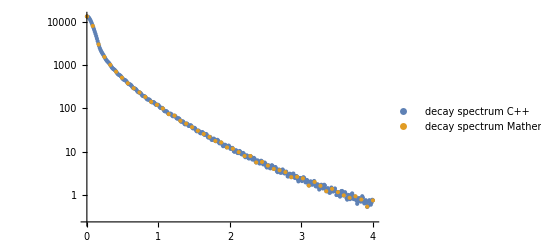

```mathematica
ListLogPlot[{Transpose@{qTscpp,primespeclistcpp},Transpose@{qTstest,dccspectest}},PlotLegends->{"decay spectrum C++","decay spectrum Mathematica"}]
```